```mathematica
a=Range[{x,y},{x+7,y}]
```

{{x,1+x,2+x,3+x,4+x,5+x,6+x,7+x},{y}}

```mathematica
b=Range[a/.x->1,a/.x->5]
```

{{1,2,3,4,5},{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9},{6,7,8,9,10},{7,8,9,10,11},{8,9,10,11,12}}

```mathematica
A=Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
B=Range[5]
```

{1,2,3,4,5}

```mathematica
Table[A,B]
```

{{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8}}

```mathematica
Range[{1,1},{8,5}]
```

{{1,2,3,4,5,6,7,8},{1,2,3,4,5}}

```mathematica
ij=Table[{i,j},{i,1,8},{j,1,5}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5}},{{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3,3},{3,4},{3,5}},{{4,1},{4,2},{4,3},{4,4},{4,5}},{{5,1},{5,2},{5,3},{5,4},{5,5}},{{6,1},{6,2},{6,3},{6,4},{6,5}},{{7,1},{7,2},{7,3},{7,4},{7,5}},{{8,1},{8,2},{8,3},{8,4},{8,5}}}

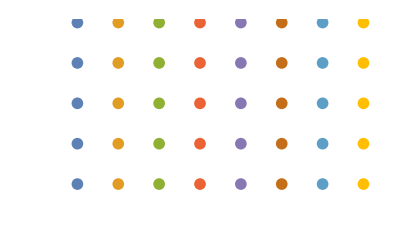

```mathematica
a=ListPlot[ij,Axes->False,PlotMarkers->{●,12}]
```

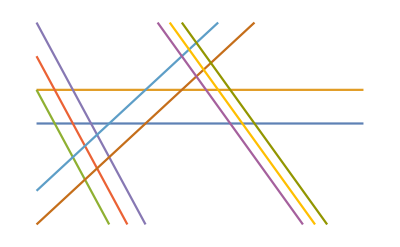

```mathematica
b=Plot[{y=3,y=4,y=-2x+4,y=-2x+5,y=-2x+6,y=x,y=x+1,y=-1.5x+11.5,y=-1.5x+11,y=-1.5x+12},{x,0,9},PlotRange->{{0,9},{0,6}},Axes->False]
```

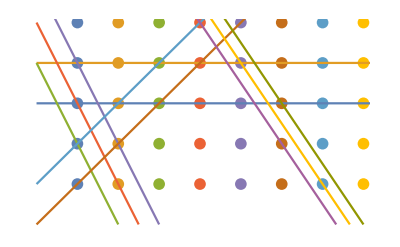

```mathematica
Show[a,b]
```